```mathematica
(*HW1.5.9,v=0.1,M=10,deltat=0.05,T=0.1,0.9,2.0*)
```

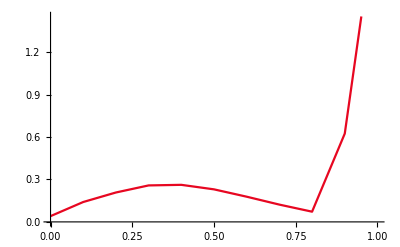
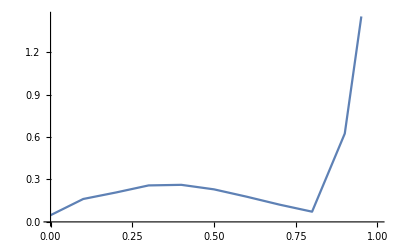
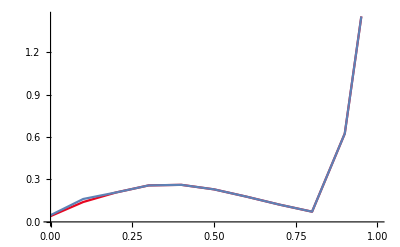
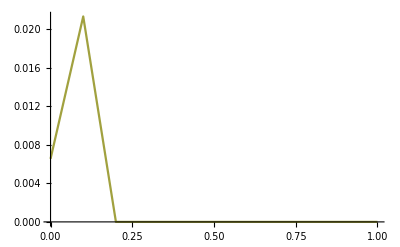

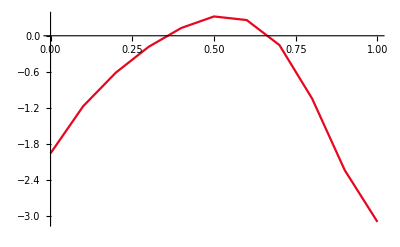
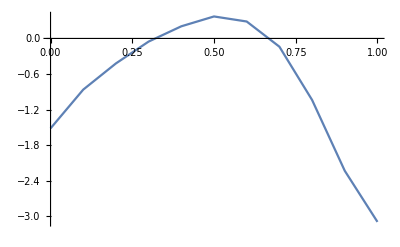
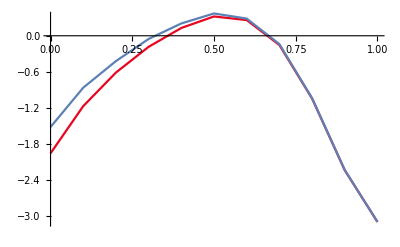
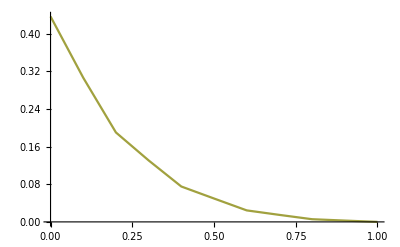

```mathematica
list1=Import["E:\\study_materials\\PDEns\\07\\first1.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second1.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
list1=Import["E:\\study_materials\\PDEns\\07\\first2.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second2.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
list1=Import["E:\\study_materials\\PDEns\\07\\first3.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second3.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
(*从左到右以此为：一阶近似，二阶近似，对比图，两种近似的差值的绝对值*)
```

```mathematica
(*HW1.5.10,v=0.1,M=20,deltat=0.01,T=0.1,0.9,2.0*)
```

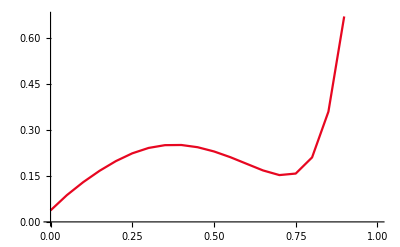
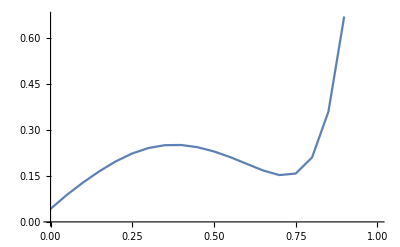
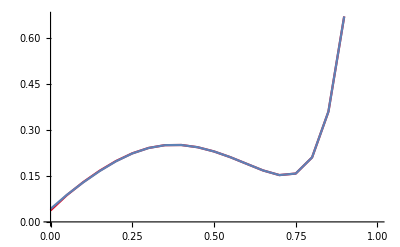
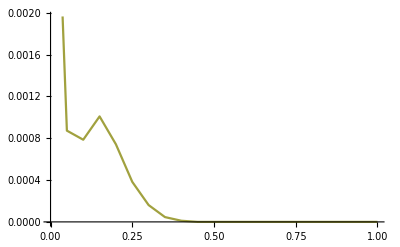

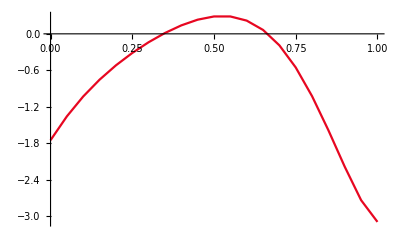
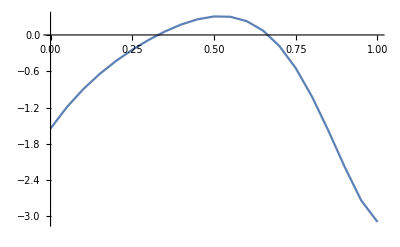
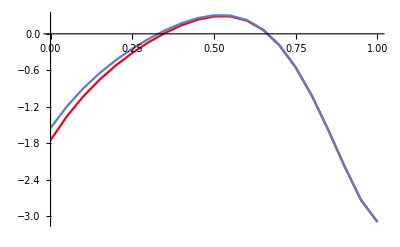
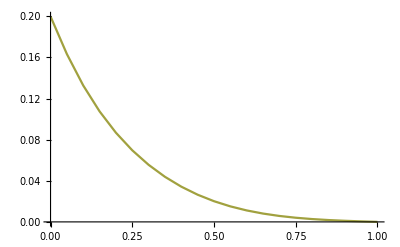

```mathematica
list1=Import["E:\\study_materials\\PDEns\\07\\first4.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second4.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
list1=Import["E:\\study_materials\\PDEns\\07\\first5.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second5.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
list1=Import["E:\\study_materials\\PDEns\\07\\first6.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second6.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
(*从左到右以此为：一阶近似，二阶近似，对比图，两种近似的差值的绝对值*)
```

```mathematica
(*HW1.5.10,v=0.1,M=40,deltat=0.002,T=0.1,0.9,2.0*)
```

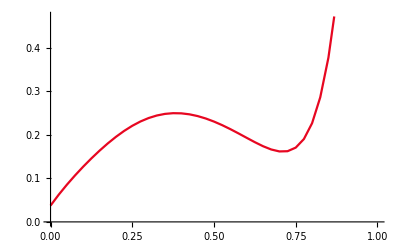
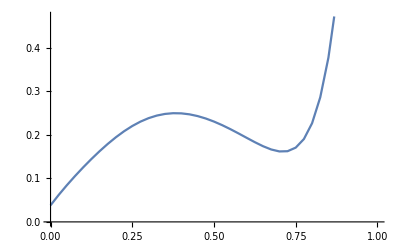
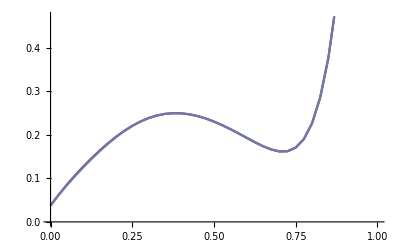
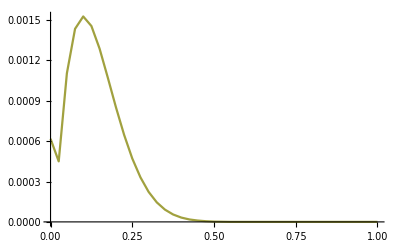

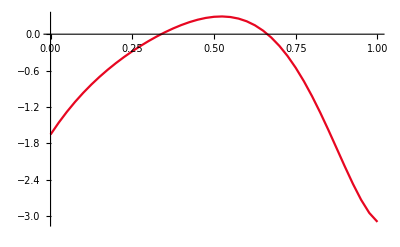
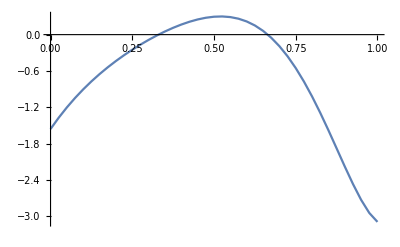
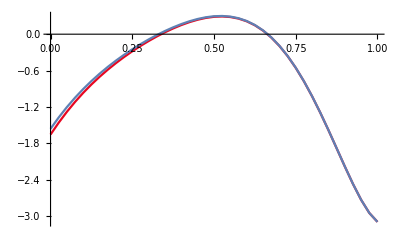
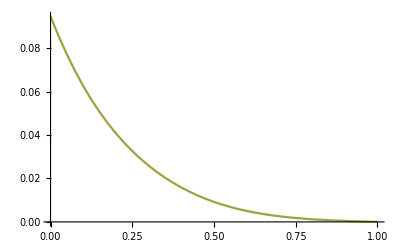

```mathematica
list1=Import["E:\\study_materials\\PDEns\\07\\first7.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second7.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
list1=Import["E:\\study_materials\\PDEns\\07\\first8.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second8.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
list1=Import["E:\\study_materials\\PDEns\\07\\first9.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\second9.txt","Table"];
list=Table[{list1[[i,1]],Abs[list1[[i,2]]-list2[[i,2]]]},{i,Length[list1]}];
{ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2],Show[ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]],ListLinePlot[list2]],ListLinePlot[list,PlotStyle->ColorData[5,"ColorList"]]}
(*从左到右以此为：一阶近似，二阶近似，对比图，两种近似的差值的绝对值*)
```

```mathematica
(*******************************************************************************************************************************************************************************)
```

```mathematica
(*HW2.2.2,v=0.1,deltax=0.1,deltat=0.005,T=0.05,0.1*)
```

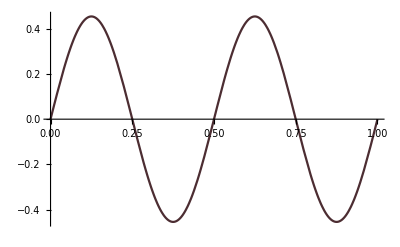
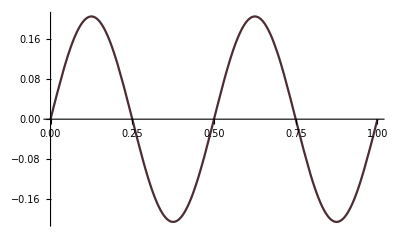

```mathematica
(*真解*)
u[x_,t_]:=E^(-1.6 Pi Pi t) Sin[4 Pi x];
img1=Plot[u[x,0.05],{x,0,1},PlotStyle->ColorData[12,"ColorList"]];
img2=Plot[u[x,0.1],{x,0,1},PlotStyle->ColorData[12,"ColorList"]];
{img1,img2}
```

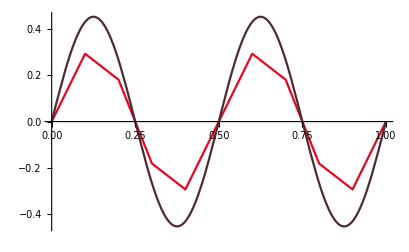
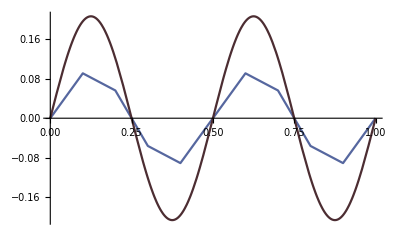

```mathematica
list1=Import["E:\\study_materials\\PDEns\\07\\output\\first10.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\output\\first11.txt","Table"];
img11=ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]];
img22=ListLinePlot[list2,PlotStyle->ColorData[2,"ColorList"]];
{Show[img11,img1,PlotRange->All],Show[img22,img2,PlotRange->All]}
(*从左到右以此为：t=0.05,t=0.1*)
```

```mathematica
(*HW2.2.2,v=0.1,deltax=0.05,deltat=0.0125,T=0.05,0.1*)
```

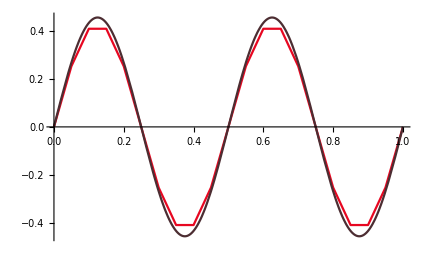
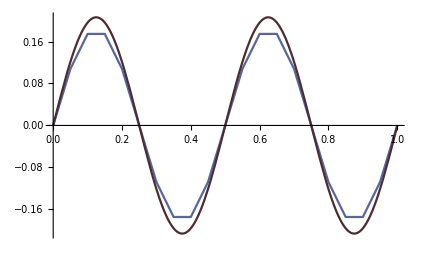

```mathematica
list1=Import["E:\\study_materials\\PDEns\\07\\output\\first12.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\output\\first13.txt","Table"];
img11=ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]];
img22=ListLinePlot[list2,PlotStyle->ColorData[2,"ColorList"]];
{Show[img11,img1,PlotRange->All],Show[img22,img2,PlotRange->All]}
(*从左到右以此为：t=0.05,t=0.1*)
```

```mathematica
(*HW2.2.2,v=0.1,deltax=0.01,deltat=0.0005,T=0.05,0.1*)
```

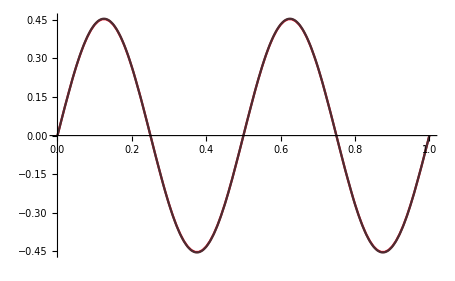
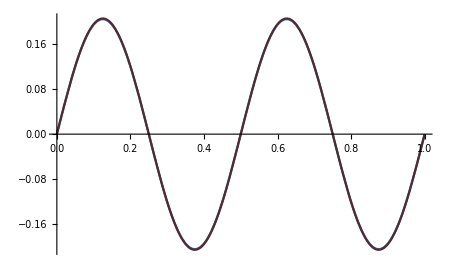

```mathematica
list1=Import["E:\\study_materials\\PDEns\\07\\output\\first14.txt","Table"];
list2=Import["E:\\study_materials\\PDEns\\07\\output\\first15.txt","Table"];
img11=ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]];
img22=ListLinePlot[list2,PlotStyle->ColorData[2,"ColorList"]];
{Show[img11,img1,PlotRange->All],Show[img22,img2,PlotRange->All]}
(*从左到右以此为：t=0.05,t=0.1*)
```